## Convergencia en distribución

#### Ejemplo: Binomial a Poisson; ℬ(n,λ/n)→^d 𝒫(λ)

Función de probabilidad de  una variable con distribución ℬ(n,λ/n)

Comando: PDF

```mathematica
PDF[BinomialDistribution[n,λ/n],x]
```

Piecewise[{{(λ/n)^x (1-λ/n)^(n-x) Binomial[n,x], 0≤x≤n}, {0, True}}]

Función de distribución

Comando: CDF

```mathematica
CDF[BinomialDistribution[n,λ/n],x]
```

Piecewise[{{BetaRegularized[1-λ/n,n-Floor[x],1+Floor[x]], 0≤x<n}, {1, x≥n}, {0, True}}]

Gráfica para 3≤n≤7 y λ=3

Comando: DiscretePlot

Opciones: ExtentSize, ExtentMarkers, Filling

Comando: Evaluate

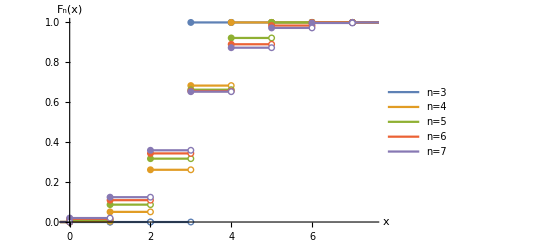

```mathematica
DiscretePlot[Evaluate[Table[CDF[BinomialDistribution[n,3/n],x],{n,3,7}],{x,-1,8}],
ExtentSize->Right,ExtentMarkers->{"Filled","Empty"},Filling->None,
PlotRange->{{-0.1,7.5},All},AxesOrigin->{0,0},AxesLabel->{x,Subscript[F, n][x]},PlotLegends->Table[TextCell[Row[{"n=",n}]],{n,3,7}]
]
```

Límite débil de F_n (En este caso, el límite de la función de probabilidad lleva al límite de la función de distribución)

Comando: DiscreteLimit

```mathematica
fplimite[λ_,x_]:=DiscreteLimit[PDF[BinomialDistribution[n,λ/n],x],n->∞]
```

```mathematica
fplimite[λ,x]
```

Piecewise[{{(ⅇ^-λ λ^x)/Gamma[1+x], x≥0}, {0, True}}]

Función de probabilidad de una variable con distribución 𝒫(λ)

```mathematica
PDF[PoissonDistribution[λ],x]
```

Piecewise[{{(ⅇ^-λ λ^x)/(x!), x≥0}, {0, True}}]

Construcción de un modelo discreto a partir de la función de probabilidad

Comando: ProbabilityDistribution

Rango: {x,0,∞,1}

```mathematica
Modelolimite[λ_]:=ProbabilityDistribution[fplimite[λ,x],{x,0,∞,1}]
```

```mathematica
PDF[Modelolimite[λ],x]
```

Piecewise[{{(ⅇ^-λ λ^x)/Gamma[1+x], x≥0}, {0, True}}]

```mathematica
CDF[Modelolimite[λ],x]
```

Piecewise[{{ⅇ^-λ, x==0}, {(-Gamma[1+Floor[x]]-Floor[x] Gamma[1+Floor[x]]+Gamma[2+Floor[x]]+Gamma[1+Floor[x],λ]+Floor[x] Gamma[1+Floor[x],λ])/Gamma[2+Floor[x]], x>0}, {0, True}}]

```mathematica
FullSimplify[Piecewise[{{ⅇ^-λ,x==0},{(-Gamma[1+Floor[x]]-Floor[x] Gamma[1+Floor[x]]+Gamma[2+Floor[x]]+Gamma[1+Floor[x],λ]+Floor[x] Gamma[1+Floor[x],λ])/Gamma[2+Floor[x]],x>0}},0]]
```

Piecewise[{{Gamma[1+Floor[x],λ]/(Floor[x]!), x≥0}, {0, True}}]

```mathematica
CDF[PoissonDistribution[λ],x]
```

Piecewise[{{GammaRegularized[1+Floor[x],λ], x≥0}, {0, True}}]

Q(a, z) = (Γ(a, z))/(Γ(a)).  Q es la función gamma regularizada y Γ(a, z)=∫_z^∞ t^(a-1)e^-t dt es la función gamma incompleta

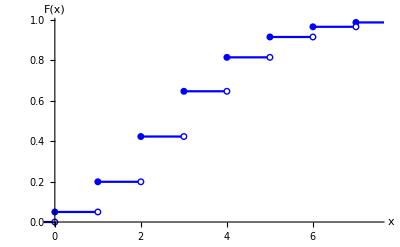

```mathematica
DiscretePlot[Piecewise[{{Gamma[1+Floor[x],3]/(Floor[x]!),x≥0}},0],{x,-1,7},ExtentSize->Right,ExtentMarkers->{"Filled","Empty"},Filling->None,PlotStyle->Blue,PlotRange->{{-0.1,7.5},Automatic},AxesOrigin->{0,0},AxesLabel->{x,F[x]}]
```

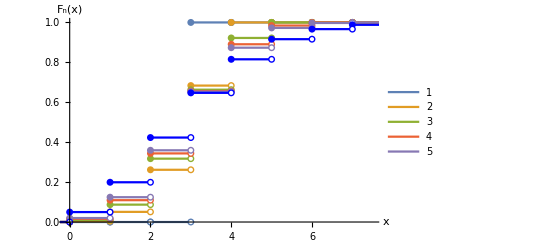

```mathematica
Show[%7,%25]
```